```mathematica
Clear["Global`*"]
```

### Constants and Parameters

```mathematica
kB=1.38 10^-23;(*Boltzmann-constant*)
T=273+21; (*temperature of the cell*)
c=3 10^8; (*Speed of light*)
d12=3.5 10^-29; (*dipole-moment for D2 line Rb*)
hbar= 1.054 10^-34; 
ep0=8.854 10^-12;
mass=1.443 10^-25;
muB=9.274*10^-28;(*J G^-1 Bohr's magneton*)
Γ= 2π  6 10^6;(*Spontaneous decay rate*)
K = N@((2 π)/(780 10^-9))(*Wave number*)
```

8.05537×10^6

### Scaling to dimension less variables

```mathematica
x= K/Γ;
maxx= x 300;
scaledvrms =√((kB T K^2)/(mass Γ^2)) 
MB[v_]:= 1/(√(2 π)scaledvrms) Exp[-v^2/(2 scaledvrms^2)]
```

35.829

### Hamiltonian and decay matrices

```mathematica
Subscript[ρ,{i1_,i2_}]:=ρ[i1,i2]
H={{0,0, 0.5 Ωp },{0,-(δp-δc),  0.5Ωc},{  0.5Ωp,  0.5 Ωc,-(δp -y)}};
rhomatrix=Table[Subscript[ρ,{i,j}],{i,1,3},{j,1,3}];
anticommutatormatrix={{γ (Subscript[ρ,{3,3}])+γp(Subscript[ρ,{2,2}]-Subscript[ρ,{1,1}]),-(γp+γd)Subscript[ρ,{1,2}],-(γ+0.5γp+0.5γd)Subscript[ρ,{1,3}]},{(-γp-γd)Subscript[ρ,{2,1}],γ( Subscript[ρ,{3,3}])+γp(Subscript[ρ,{1,1}]-Subscript[ρ,{2,2}]),-(γ+0.5γp+0.5γd)Subscript[ρ,{2,3}]},{-(γ+0.5γp+0.5γd)Subscript[ρ,{3,1}],-(γ+0.5γp+0.5γd)Subscript[ρ,{3,2}],-2γ Subscript[ρ,{3,3}]}};
rhomatrix1= Flatten[rhomatrix];
commutatormatrix= Dot[H,rhomatrix]-Dot[rhomatrix,H];
Solutionlist=Flatten[Table[FullSimplify[Solve[0==I(commutatormatrix[[i,j]])+anticommutatormatrix[[i,j]],rhomatrix[[i,j]]]],{i,1,3},{j,1,3}]];
```

```mathematica
Clear[Ωp,Ωc,δp,δc,γ ,γp,γd];
γ=1;
γp=γd =0.001;
Ωc=2 ;
Ωp=0.05 ;
δc=0;
y=m;
new=ParallelTable[equations=Table[First[Solutionlist[[i]]]==Last[Solutionlist[[i]]],{i,1,9}];
equations1=Join[equations,{ρ[1,1]+ρ[2,2]+ρ[3,3]==1}];
table1=Table[{δp,Im[-Last[Solve[equations1,rhomatrix1][[1,3]]]]},{δp,-5,5,0.01}];
table1,{m,Range[-50,50,0.1]}];

(*SetSharedVariable[new];
new={};
ParallelDo[
equations=Table[First[Solutionlist[[i]]]==Last[Solutionlist[[i]]],{i,1,9}];
equations1=Join[equations,{ρ[1,1]+ρ[2,2]+ρ[3,3]==1}];
table1=Table[{δp,Im[-Last[Solve[equations1,rhomatrix1][[1,3]]]]},{δp,-5,5,0.01}];
AppendTo[new, table1] ,
{m,Range[-50, 50,0.1]}
]*)
```

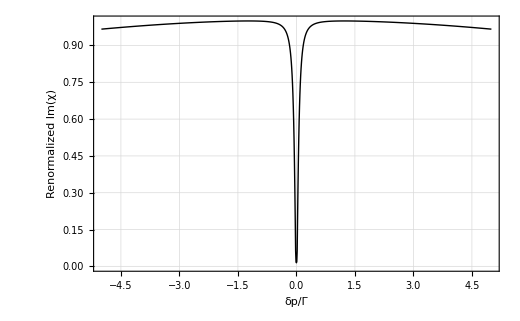

```mathematica
t1 =Table[MB[i],{i,-50,50,0.1}];
t2= Table[i,{i,-5,5,0.01}];
t3=t1.(new[[All,All,2]]);
(*t3 =Table[Sum[t1[[i]]*new[[i,j,2]],{i,1,Length[t1]}],{j,1,Length[t2]}];*)
t4= Table[{t2[[i]],t3[[i]]},{i,1,Length[t2]}];
maxY=Max[t4[[All,2]]];
normalizedTable1={#[[1]],#[[2]]/maxY}&/@t4;
plot1=ListLinePlot[normalizedTable1,PlotStyle->{Directive[Black,Thick]},
Frame->True,
Axes->False,
ImageSize->520,
PlotRange->All,
TicksStyle->Directive[Bold,14],
FrameStyle->Directive[Black],
LabelStyle->Directive[Black,Bold,12],(*bold,large labels*)
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->Automatic,
ImagePadding->{{Automatic,Automatic},{Automatic,Scaled[0.01]}},
FrameLabel->{Style["δp/Γ",Bold,16],Style["Renormalized Im(χ)",Bold,16]}]
```

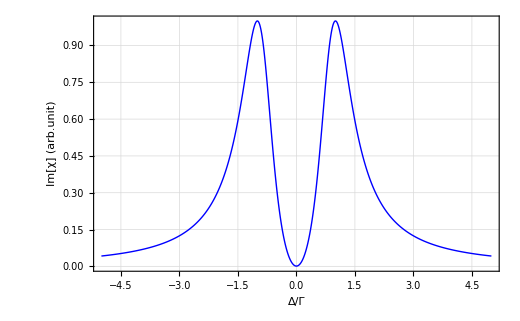

```mathematica
table2=new[[501]];
maxyy=Max[table2[[All,2]]];
normalizedTable2={#[[1]],#[[2]]/maxyy}&/@table2;
plot2=ListLinePlot[normalizedTable2,PlotStyle->{Directive[Blue,Thick]},
Frame->True,
Axes->False,
ImageSize->520,
PlotRange->All,
TicksStyle->Directive[Bold,14],
FrameStyle->Directive[Black],
LabelStyle->Directive[Black,Bold,12],(*bold,large labels*)
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->Automatic,
ImagePadding->{{Automatic,Automatic},{Automatic,Scaled[0.01]}},
FrameLabel->{Style["Δ/Γ",Bold,14],Style["Im[χ] (arb.unit)",Bold,14]}]
```

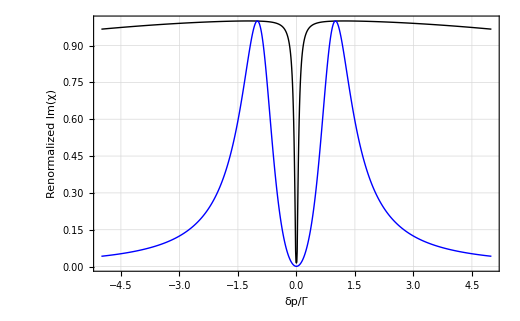

```mathematica
p1= Show[plot1,plot2,PlotRange->All]
```

```mathematica
Export["/home/nayan/Desktop/diagrams/for thesis/3level/probedoppler1.pdf",p1, ImageResolution->300];
```

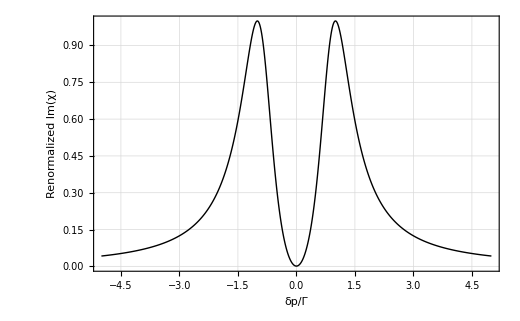

```mathematica
table4=new[[501]];
maxy4=Max[table4[[All,2]]];
normalizedTable4={#[[1]],#[[2]]/maxy4}&/@table4;
plot4=ListLinePlot[normalizedTable4,PlotStyle->{Directive[Black,Thick]},
Frame->True,
Axes->False,
ImageSize->520,
PlotRange->All,
TicksStyle->Directive[Bold,14],
FrameStyle->Directive[Black],
LabelStyle->Directive[Black,Bold,12],(*bold,large labels*)
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->Automatic,
ImagePadding->{{Automatic,Automatic},{Automatic,Scaled[0.01]}},
FrameLabel->{Style["δp/Γ",Bold,16],Style["Renormalized Im(χ)",Bold,16]}]
```

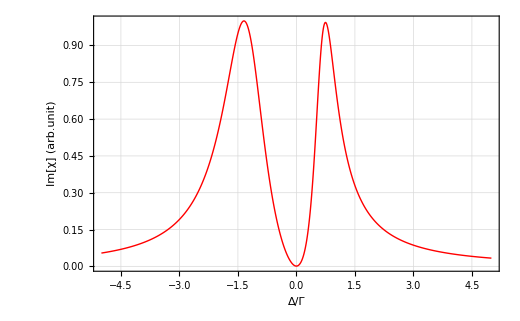

```mathematica
table5=new[[495]];
maxy5=Max[table5[[All,2]]];
normalizedTable5={#[[1]],#[[2]]/maxy5}&/@table5;
plot5=ListLinePlot[normalizedTable5,PlotStyle->{Directive[Red,Thick]},
Frame->True,
Axes->False,
ImageSize->520,
PlotRange->All,
TicksStyle->Directive[Bold,14],
FrameStyle->Directive[Black],
LabelStyle->Directive[Black,Bold,12],(*bold,large labels*)
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->Automatic,
ImagePadding->{{Automatic,Automatic},{Automatic,Scaled[0.01]}},
FrameLabel->{Style["Δ/Γ",Bold,14],Style["Im[χ] (arb.unit)",Bold,14]}]
```

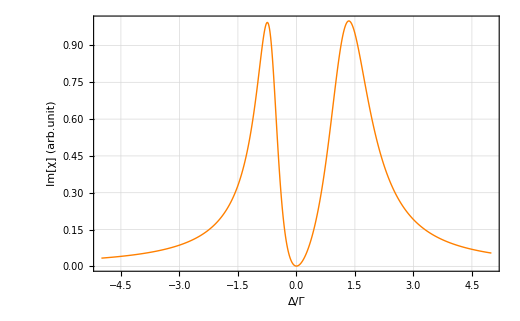

```mathematica
table6=new[[507]];
maxy6=Max[table6[[All,2]]];
normalizedTable6={#[[1]],#[[2]]/maxy6}&/@table6;
plot6=ListLinePlot[normalizedTable6,PlotStyle->{Directive[Orange,Thick]},
Frame->True,
Axes->False,
ImageSize->520,
PlotRange->All,
TicksStyle->Directive[Bold,14],
FrameStyle->Directive[Black],
LabelStyle->Directive[Black,Bold,12],(*bold,large labels*)
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->Automatic,
ImagePadding->{{Automatic,Automatic},{Automatic,Scaled[0.01]}},
FrameLabel->{Style["Δ/Γ",Bold,14],Style["Im[χ] (arb.unit)",Bold,14]}]
```

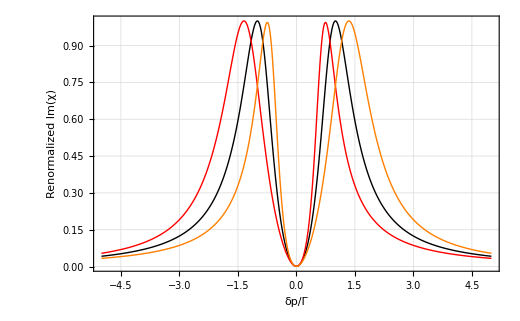

```mathematica
p=Show[plot4,plot5,plot6,PlotRange->All]
```

```mathematica
Export["/home/nayan/Desktop/diagrams/for thesis/3level/probedoppler2.pdf",p, ImageResolution->300];
```

```mathematica
6/x
```

28.08